Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2023/24
F.Javier Muñoz Delgado

# Notas y Prácticas del Tema 8: Funciones de varias variables II (Derivadas, Extremos, Integrales)

## Introducción Derivadas parciales Plano tangente a la gráfica de una función de dos variables Aproximación de una función por el plano tangente Estimación de errores

Para calcular las derivadas de una función de varias variables podemos usar la instrucción D y también la paleta.

```mathematica
f[x_,y_,z_]:= 3x^2 y + Cos[y*z]+Sin[x]*y^2
```

```mathematica
g[x_,y_]:= x^2+y^2
```

```mathematica
D[f[x,y,z],{x,1},{y,2}]
```

2 Cos[x]

```mathematica
D[g[x,y], x]
```

2 x

También podemos evaluar en un punto determinado.

```mathematica
D[f[x,y,z],{x,1},{y,2}]/.{x->1,y->2,z->-1}
```

2 Cos[1]

Plano tangente a la gráfica de g[x, y] en el punto (1, 2).
La fórmula es similar a la de la recta tangente (recordemos y=f(x0)+f ’(x0)(x-x0) ) añadiendo un nuevo sumando al haber dos derivadas parciales.
z=g(1,2) + ∂_x g(1,2) (x-1)+∂_y g(1,2) (y-2)

El vector gradiente en ese punto es el vector  (∂_x g(1,2) , ∂_y g(1,2)) y muestra la dirección de mayor crecimiento de la función g(x,y) en ese punto.

```mathematica
g[1,2]+(D[g[x,y],x]/.{x->1,y->2}) (x-1)+(D[g[x,y],y]/.{x->1,y->2}) (y-2)
```

5+2 (-1+x)+4 (-2+y)

El vector gradiente marca una dirección perpendicular a las curvas de nivel.

```mathematica
Show[ContourPlot[g[x,y]==g[1,2],{x,0,2},{y,1,3}],ParametricPlot[{1,2}+t{(D[g[x,y],x]/.{x->1,y->2}) ,(D[g[x,y],y]/.{x->1,y->2})},{t,-1,1}],ListPlot[{{1,2}}],AspectRatio->Automatic]
```

-Graphics-

Podemos dibujar la gráfica de la función y del plano tangente.

```mathematica
Plot3D[{g[x,y],5+2 (-1+x)+4 (-2+y)},{x,-2,4},{y,-2,4}]
```

-Graphics3D-

El plano tangente nos sirve también para estimar el valor de la función en puntos cercanos al punto de tangencia. Evaluemos la función y el plano tangente en el punto (0.95, 2.01)

```mathematica
g[0.95,2.01]
```

4.9426

```mathematica
5+2 (-1+x)+4 (-2+y)/.{x->0.95,y->2.01}
```

4.94

Estimación de errores
Supongamos que queremos conocer el área de un rectángulo. El área sería la función f(x,y)=xy donde x e y son las longitudes de los lados del rectángulo. Si medimos los lados y obtenemos x=20 y=40, el área será 20*40=800.
Si la cinta métrica con la que medimos tiene un margen de error de 0.5, cuál sería el error que podríamos tener en el área.

Con el plano tangente tendríamos que f(x,y) se aproximaría por f(20,40) + ∂_x f(20,40) (x-20)+∂_y f(20,40) (y-40)
como ∂_x f(x,y)=y, ∂_y f(x,y)=x, tenemos que ∂_x f(20,40)=40, ∂_y f(20,40)=20.
Si la diferencia entre el valor real x y el valor medido 20 es menor que 0.5, e igualmente para y, tenemos que el error
|f(x,y)-f(20,40)| se podría estimar por |∂_x f(20,40)| 0.5 + |∂_y f(20,40)| 0.5=40*0.5+20*0.5=20+10=30.
En este caso, al ser la parcial respecto de x mayor, el error en la x introduce un mayor error en la función.
El error en las mediciones podría traer como consecuencia que el valor calculado del área, 800, tenga un error estimado de hasta 30.

Esta estimación del error se podría mejorar utilizando también derivadas de orden superior.

Otro ejemplo:
El índice de masa corporal se define como el cociente entre el peso (medido en kilogramos) y la altura (medida en metros) elevada al cuadrado, I=M/H^2. 

Supongamos que la báscula nos da un peso de 80Kg. y que la cinta métrica nos da un valor de 1.7 m. Si la báscula tiene un margen de error de 1 kg y la cinta métrica un error de 2 cms, calcular el error que cada medida puede inducir en el índice de masa corporal. ¿Cuál puede inducir más error? o ¿qué aparato deberíamos cambiar antes?

```mathematica
F[M_,H_]:=M/H^2
```

```mathematica
F[80,1.7]
```

27.6817

```mathematica
1*D[F[M,H],M]/.{M->80,H->1.7}
```

0.346021

```mathematica
0.02*D[F[M, H], H] /. {M -> 80, H -> 1.7}
```

-0.651333

El índice de masa corporal calculado es 27.6817. La báscula puede introducir un error de 0.346021, mientras que la cinta métrica podría introducir un error de 0.651333. Por tanto, la cinta métrica induce un error mayor (sería lo más urgente en cambiar). La estimación del error debido a los datos erróneos puede llegar a 0.346021+0.651333=0.997354.

## Cálculo de máximos y de mínimos (y de puntos de silla). Extremos relativos

Al igual que con funciones de una variable, podemos preguntarnos por los máximos y mínimos de una función de varias variables.

Una posibilidad es buscar máximos o mínimos locales. Se trata de puntos donde la función es mayor o igual (o menor o igual) que en todos los de un entorno del punto. Como las funciones suelen ser derivables, la herramienta que se utiliza en este caso es la derivada. Los puntos interiores del dominio de una función derivable que sean máximos o mínimos locales, lo serán en cada una de las variables, por tanto tendrán todas las derivadas igual a cero. Por ello, derivamos y buscamos los posibles puntos.

Otra posibilidad es buscar máximos o mínimos absolutos en conjuntos cerrados y acotados. En esta situación, basta que la función sea continua para tener la seguridad de que existirán (Teorema de Weiertrass). Para encontrarlos, distinguimos los puntos del interior y el borde. En el interior estarían en puntos donde la derivada se anule, o en puntos donde la función no sea derivable.

Consideremos las funciones f1(x,y) = x^2+ y^2, f2(x,y) = x^2- y^2, f3(x,y) = -x^2- y^2, f4(x,y) = x^4+ y^4, y busquemos sus extremos relativos.

```mathematica
f1[x_,y_]:= x^2+ y^2
```

```mathematica
Solve[{D[f1[x,y],x]==0,D[f1[x,y],y]==0},{x,y}]
```

{{x→0,y→0}}

El punto (0,0) es un punto crítico (candidato a ser máximo, mínimo o punto de silla). Intentamos averiguarlo calculando el hessiano de la función en el punto (0,0)

```mathematica
Det[({{D[f1[x,y], x,x], D[f1[x,y], x,y]}, {D[f1[x,y], x,y], D[f1[x,y], y,y]}})]/.{x->0,y->0}
```

4

Como el hessiano es mayor que cero, significa que habrá un máximo o un mínimo local. Para saber qué es, estudiamos el signo de la derivada segunda (en la x o en la y).

```mathematica
D[f1[x,y],{x,2}]/.{x->0,y->0}
```

2

Al ser positiva se trata de un mínimo.

```mathematica
f2[x_,y_]:= x^2- y^2
```

```mathematica
Solve[{D[f2[x,y],x]==0,D[f2[x,y],y]==0},{x,y}]
```

{{x→0,y→0}}

El punto (0,0) es un punto crítico (candidato a ser máximo, mínimo o punto de silla). Intentamos averiguarlo calculando el hessiano de la función en el punto (0,0)

```mathematica
Det[({{D[f2[x,y], x,x], D[f2[x,y], x,y]}, {D[f2[x,y], x,y], D[f2[x,y], y,y]}})]/.{x->0,y->0}
```

-4

Como el hessiano es menor que cero, significa que habrá un punto de silla.

```mathematica
f3[x_,y_]:= -x^2- y^2
```

```mathematica
Solve[{D[f3[x,y],x]==0,D[f3[x,y],y]==0},{x,y}]
```

{{x→0,y→0}}

El punto (0,0) es un punto crítico (candidato a ser máximo, mínimo o punto de silla). Intentamos averiguarlo calculando el hessiano de la función en el punto (0,0)

```mathematica
Det[({{D[f3[x,y], x,x], D[f3[x,y], x,y]}, {D[f3[x,y], x,y], D[f3[x,y], y,y]}})]/.{x->0,y->0}
```

4

Como el hessiano es mayor que cero, significa que habrá un máximo o un mínimo local. Para saber qué es estudiamos el signo de la derivada segunda (en la x o en la y).

```mathematica
D[f3[x,y],{x,2}]/.{x->0,y->0}
```

-2

Al ser negativa se trata de un máximo.

```mathematica
f4[x_,y_]:= x^4+ y^4
```

```mathematica
Solve[{D[f4[x,y],x]==0,D[f4[x,y],y]==0},{x,y}]
```

{{x→0,y→0}}

El punto (0,0) es un punto crítico (candidato a ser máximo, mínimo o punto de silla). Intentamos averiguarlo calculando el hessiano de la función en el punto (0,0)

```mathematica
Det[({{D[f4[x,y], x,x], D[f4[x,y], x,y]}, {D[f4[x,y], x,y], D[f4[x,y], y,y]}})]/.{x->0,y->0}
```

0

Como el hessiano es cero, este criterio no nos da información.

Veamos las gráficas de las funciones estudiadas.

```mathematica
{Plot3D[f1[x,y],{x,-2,2},{y,-2,2}],Plot3D[f2[x,y],{x,-2,2},{y,-2,2}],Plot3D[f3[x,y],{x,-2,2},{y,-2,2}],Plot3D[f4[x,y],{x,-2,2},{y,-2,2}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

En el caso de f1 tenemos un mínimo, en el de f2 un punto de silla, en el de f3 un máximo y en el de f4 hay un mínimo, aunque el criterio no nos dio información. Si en lugar de f4, hubiésemos estudiado las funciones x^4- y^4 o -x^4- y^4, el criterio del hessiano no nos daría información, siendo el primer ejemplo un punto de silla y el segundo un máximo.

Este criterio es similar al que teníamos de la derivada segunda en funciones de una variable. Si la derivada segunda era mayor que cero había un mínimo, si era menor que cero había un máximo, pero si era cero no podíamos concluir nada.

Veamos otro ejemplo. Calcular los extremos de la función f(x,y).

```mathematica
f[x_,y_]:=y^3+x^2 y + 2 x^2 + 2 y^2-4y-8
```

```mathematica
Solve[{D[f[x,y],x]==0,D[f[x,y],y]==0},{x,y}]
```

{{x→0,y→-2},{x→0,y→2/3},{x→0,y→-2}}

Los puntos (0, -2) y (0, 2/3) son puntos críticos (Candidatos a ser máximos, mínimos o puntos de silla). Para evaluar el hessiano en diferentes puntos, definimos la función hessiano.

```mathematica
hess[x_,y_]:=Det[({{D[f[u,v], u,u], D[f[u,v], u,v]}, {D[f[u,v], u,v], D[f[u,v], v,v]}})]/.{u->x,v->y}
```

```mathematica
{hess[0,-2],hess[0,2/3]}
```

{0,128/3}

El hessiano en el (0,-2) es cero y no nos da información. En el punto (0,2/3) el hessiano es positivo y habrá máximo o mínimo. Para saberlo evaluamos la derivada segunda en la primera o la segunda variable.

```mathematica
D[f[u,v], u,u]/.{u->0,v->2/3}
```

16/3

La función en (0, 2/3) tiene un mínimo local. En el punto (0, -2) no sabemos con la prueba del Hessiano si tiene máximo, mínimo o punto de silla.

```mathematica
Plot3D[f[x,y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

## Extremos absolutos (Multiplicadores de Lagrange)

Supongamos ahora el mismo problema con la condición de que x^2 + y^2 ≤ 1. En este caso el conjunto donde vamos a estudiar la función es cerrado y acotado, y al ser la función continua, tendremos máximos y mínimos absolutos. Estos podrán estar dentro o en el borde. 

1) Dentro: Para estudiar posibles máximos o mínimos dentro, y dado que la función es derivable, calculamos sus derivadas parciales e igualamos a cero.

```mathematica
Plot3D[Which[x^2+y^2≤1,f[x,y]],{x,-1,1},{y,-1,1},PlotPoints->100]
```

-Graphics3D-

```mathematica
Solve[{D[f[x,y],x]==0,D[f[x,y],y]==0},{x,y}]
```

{{x→0,y→-2},{x→0,y→2/3},{x→0,y→-2}}

El punto (0, -2) está fuera del disco (o no cumple la condición). Queda como candidato el punto (0,2/3).

2) Borde: También podría estar en la frontera, el borde del disco (cuando x^2 + y^2 = 1).

Para estudiar los máximos y mínimos en el borde, es decir, sujetos a esa condición, podemos utilizar la técnica de los multiplicadores de Lagrange. 

	2.1) Multiplicadores de Lagrange: Se trata de reunir en una misma función, la función f y la condición de estar en el borde.

```mathematica
F[x_,y_,t_]:= f[x,y]+t (x^2+y^2-1)
```

```mathematica
Solve[{D[F[x,y,t],x]==0,D[F[x,y,t],y]==0,D[F[x,y,t],t]==0},{x,y,t}]
```

{{x→0,y→-1,t→-5/2},{x→0,y→1,t→-3/2}}

Al hacer las derivadas parciales e igualar a cero, tenemos como puntos candidatos (0, 1), (0, -1).

Reuniendo todos los puntos candidatos tenemos (0,2/3), (0,1), (0,-1). Ahora evaluamos la función y vemos dónde vale más y dónde vale menos.

```mathematica
{f[0,2/3],f[0,1],f[0,-1]}//N
```

{-9.48148,-9.,-3.}

El máximo de la función se alcanza en el punto (0,-1) y es -3. El mínimo se alcanza en el punto (0,2/3) y vale -9.48.

	2.2) Otra forma: despejando
En algunos casos, en lugar de usar la técnica de los Multiplicadores de Lagrange, podríamos dejar la función en el borde con una sola variable. Para ello podríamos tratar de despejar x ó y, en función de la otra variable y sustituir en la función f.

Por ejemplo, en este caso x^2 + y^2 = 1, por tanto x^2 = 1 - y^2. Sustituyendo:
f(x,y)=y^3+x^2 y + 2 x^2 + 2 y^2-4y-8 =  y^3+(1-y^2) y + 2 (1-y^2) + 2 y^2-4y-8 = -3 (2+y) = g(y)

Obtenemos una función que depende ahora de una sola variable, y. En el borde, x^2 + y^2 = 1, la variable y se mueve en el intervalo [-1,1]. Por tanto, deberíamos buscar los máximos y mínimos de g(y) en el intervalo [-1,1]. Ahora tenemos un problema de máximos y mínimos absolutos en una variable. La función es continua en un intervalo cerrado y acotado. Como la derivada g’(y) =-3, no es cero, no tenemos candidatos del interior del intervalo. Al ser derivable sólo nos quedan como candidatos los extremos del intervalo, y=1, -1. Dado que x^2 + y^2 = 1, cuando y=1, x debe ser 0. Igualmente, si y=-1, x=0. Por tanto, los puntos candidatos que encontramos son (0,1) y (0,-1).
Los candidatos son (0,1), (0,-1), (0,2/3).

	2.3) Otra forma más: parametrizando
Se trataría de parametrizar el borde, es decir, recorrer los puntos del borde, en función de un parámetro. Los puntos de la circunferencia x^2 + y^2 = 1, pueden parametrizarse escribiendo los puntos de la forma (cos t, sen t) con t moviéndose en [0,2π]. Ahora evaluamos la función f en estos puntos y obtendremos una función de una sola variable.

```mathematica
f[Cos[t],Sin[t]]//Simplify
```

-3 (2+Sin[t])

El problema ahora es buscar los máximos y mínimos de g(t)=-3(2 + sen t) con t en [0,2π]. Como es habitual, buscamos dentro del intervalo puntos con derivada cero, y también consideramos los extremos.

```mathematica
g[t_]:=-3(2+Sin[t])
```

```mathematica
Solve[g'[t]==0,t]
```

{{t→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{t→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]}}

Obtenemos los valores de t=-π/2 y t=π/2. Los extremos del intervalo son t=0, y t= 2π. Estos puntos se corresponden en el borde con (cos (-π/2) , sen(-π/2) )=(0,-1), (cos (π/2) , sen(π/2) )=(0,1), (cos (0) , sen(0) )=(1,0), (cos (2π) , sen(2π) )=(1,0). El último punto se repite.
Ahora evaluamos la función en los puntos posibles y vemos el máximo y/o el mínimo.

```mathematica
{f[0,2/3],f[0,-1],f[0,1],f[1,0]}//N
```

{-9.48148,-3.,-9.,-6.}

## Integrales dobles

Cálculo de integrales dobles en diferentes recintos del plano. 

El caso más sencillo es el de un rectángulo de lados paralelos a los ejes, pues en ese caso cada variable se mueve en un intervalo y son independientes una de otra.

```mathematica
f[x_,y_]:= x y
```

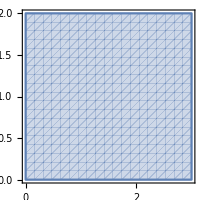

```mathematica
RegionPlot[0≤x≤3&&0≤y≤2,{x,0,3},{y,0,2},AspectRatio->Automatic]
```

Se trata de un rectángulo del plano de lados paralelos a los ejes. La variable x se mueve entre 0 y 3, mientras que la variable y se mueve entre 0 y 2.

```mathematica
∫_0^3 ∫_0^2 f[x,y]ⅆyⅆx
```

9

```mathematica
Integrate[Integrate[f[x,y],{x,0,3}],{y,0,2}]
```

9

El valor calculado es el volumen de la región en el espacio dada por la variable x entre 0 y 3, la variable y entre 0 y 2, y la variable z entre 0 y f(x,y)=xy.

El valor medio sería el correspondiente a dividir el valor obtenido (9) entre la superficie del dominio ( en este caso el rectángulo [0,3]x[0,2], por tanto 6). El valor medio es 9/6=3/2.

```mathematica
Show[{RegionPlot3D[0≤x≤3&&0≤y≤2&&0≤z≤x y,{x,0,3},{y,0,2},{z,0,6},AspectRatio->Automatic],Plot3D[3/2,{x,0,3},{y,0,2}]}]
```

-Graphics3D-

Un tipo de recinto más complejo sería el triángulo de vértices (0,0), (1,0), (0,1). En este caso, podemos considerar una cualquiera de las variables, por ejemplo la x. La variable x se mueve entre 0 y 1. Una vez fijado el valor de x, entre 0 y 1. El valor de y se moverá entre 0 y 1-x.

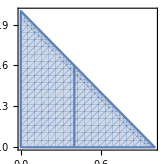

```mathematica
Show[RegionPlot[0≤x≤1&&0≤y≤1-x,{x,0,1},{y,0,1},AspectRatio->Automatic],ParametricPlot[{0.4,0.6t},{t,0,1}]]
```

La variable y se movería desde el 0 hasta el punto de la recta que une (1,0) y (0,1). Se trata de la recta x+y=1, o y=1-x.

```mathematica
∫_0^1 ∫_0^(1-x) f[x,y]ⅆyⅆx
```

1/24

```mathematica
Integrate[Integrate[f[x,y],{x,0,1-y}],{y,0,1}]
```

1/24

Un recinto más complejo es el cuadrilátero de vértices (0,0), (3,0), (4,1), (1,1).

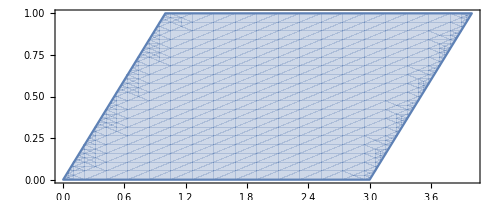

```mathematica
RegionPlot[0≤y≤1&&y≤x≤y+3,{x,0,4},{y,0,1},AspectRatio->Automatic]
```

Si decidimos considerar primero la variable x, moviéndose entre 0 y 4, nos encontramos que para ver cómo se mueve la variable y, debemos considerar tres intervalos para la x. Parece más conveniente considerar la variable y entre el 0 y el 1. Para cada valor fijado de y, estudiamos cómo se mueve la x.
Se moverá entre el recta que pasa por los puntos (0,0) y (1,1), y la recta que pasa por los puntos (3,0) y (4,1).
La primera recta es y=x, la segunda es y=x-3. Despejando x, encontramos entre qué valores se mueve.

```mathematica
∫_0^1 ∫_y^(y+3) f[x,y]ⅆxⅆy
```

13/4

Si hubiésemos considerado la variable x entre 0 y 4, habríamos tenido que calcular estas tres integrales.

```mathematica
∫_0^1 ∫_0^x f[x,y]ⅆyⅆx+∫_1^3 ∫_0^1 f[x,y]ⅆyⅆx+∫_3^4 ∫_(x-3)^1 f[x,y]ⅆyⅆx
```

13/4

Otro recinto sería el cuarto de circulo unidad centrado en el (0,0) con argumentos entre 0 y π/2 radianes.

```mathematica
RegionPlot[x^2+y^2≤ 1,{x,0,1},{y,0,1},AspectRatio->Automatic]
```

-Graphics-

Si consideramos la variable x en el intervalo [0,1], fijado x, la variable y se moverá entre 0 y el punto de la circunferencia x^2+ y^2=1. Despejando la y obtenemos, y=√(1-x^2)

```mathematica
∫_0^1 ∫_0^Sqrt[1-x^2] f[x,y]ⅆyⅆx
```

1/8

Finalmente consideremos el recinto dado por media corona circular, centrada en el punto (0,3), de radio menor 1 y radio mayor 2, con x mayor o igual que cero.

```mathematica
RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,2},{y,0,6},AspectRatio->Automatic]
```

-Graphics-

Este recinto podríamos estudiarlo de varias maneras.

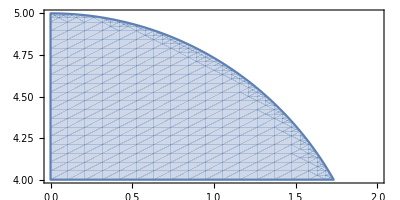
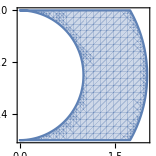
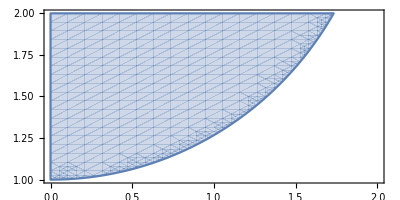

```mathematica
{RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,2},{y,4,5},AspectRatio->Automatic], RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,2},{y,2,4},AspectRatio->Automatic],
RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,2},{y,1,2},AspectRatio->Automatic]}
```

En este caso, las integrales serían

```mathematica
∫_4^5 ∫_0^Sqrt[2^2-(y-3)^2] f[x,y]ⅆxⅆy+∫_2^4 ∫_Sqrt[1^2-(y-3)^2]^Sqrt[2^2-(y-3)^2] f[x,y]ⅆxⅆy+∫_1^2 ∫_0^Sqrt[2^2-(y-3)^2] f[x,y]ⅆxⅆy
```

14

Otra forma sería,

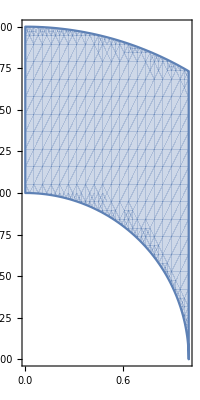
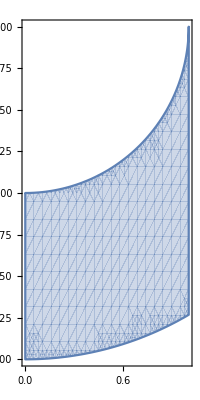
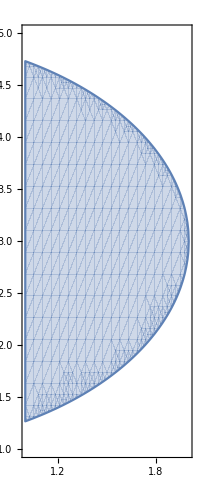

```mathematica
{RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,1},{y,3,5},AspectRatio->Automatic], RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,0,1},{y,1,3},AspectRatio->Automatic],
RegionPlot[1^2≤ x^2+(y-3)^2≤ 2^2,{x,1,2},{y,1,5},AspectRatio->Automatic]}
```

En este caso, las integrales serían

```mathematica
∫_0^1 ∫_(3+Sqrt[1^2-x^2])^(3+Sqrt[2^2-x^2]) f[x,y]ⅆyⅆx+∫_0^1 ∫_(3-Sqrt[2^2-x^2])^(3-Sqrt[1^2-x^2]) f[x,y]ⅆyⅆx+∫_1^2 ∫_(3-Sqrt[2^2-x^2])^(3+Sqrt[2^2-x^2]) f[x,y]ⅆyⅆx
```

14

Quizás la forma más sencilla sería considerar la integral en el medio disco grande y restarle la integral en el medio disco pequeño. Dado que la función f(x,y)=xy está definida en todo el plano, esto se podría hacer.

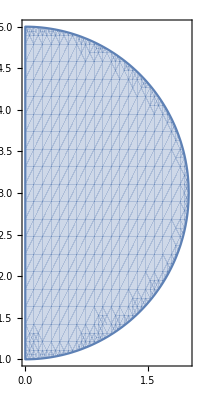
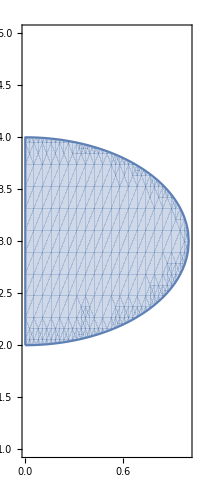

```mathematica
{RegionPlot[x^2+(y-3)^2≤ 2^2,{x,0,2},{y,1,5},AspectRatio->Automatic], RegionPlot[ x^2+(y-3)^2≤ 1^2,{x,0,1},{y,1,5},AspectRatio->Automatic]}
```

En este caso, las integrales serían

```mathematica
∫_1^5 ∫_0^Sqrt[2^2-(y-3)^2] f[x,y]ⅆxⅆy-∫_2^4 ∫_0^Sqrt[1^2-(y-3)^2] f[x,y]ⅆxⅆy
```

14

Como es lógico todos los resultados coinciden, aunque las integrales que estamos calculando pueden ser de diferente dificultad.

Para hallar los recintos y dónde se mueven cada una de las variables, tenemos que conocer la ecuación de una circunferencia si nos dan el centro (a,b) y el radio r.
(x - a)^2 + (y - b)^2=r^2
En el ejemplo anterior, teníamos dos circunferencias (la de radio 1 y la de radio 2) y para cada recinto debíamos despejar una de las variables de alguna de las ecuaciones.
Igualmente, es importante poder calcular la ecuación de una recta que pasa por dos puntos.

## 6.- Calcular la integral de la función f(x,y)= 2 x^2+3y en el triángulo de vértices (1,1), (2,3) y (5,3). Enero 22

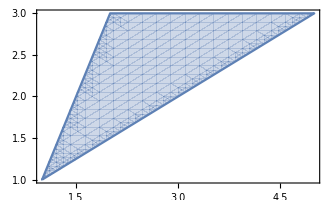
Solución:
Las rectas que pasan por los vértices son:
(2,3) y (5,3): y=3.
(1,1) y (2,3): y=2x-1, o lo que es lo mismo, x=(y+1)/2.
(1,1) y (5,3): y=(x+1)/2, o lo que es lo mismo, x= 2y-1.

-Graphics-
Observando la región, vemos que si consideramos la variación de la y, en el intervalo [1,3], podemos dejar la x variando en [(y+1)/2, 2y-1]. Así tenemos que calcular una sola integral doble: 
∫_1^3 (∫_((y+1)/2)^(2y-1) 2 x^2+3yⅆx)ⅆy=∫_1^3 (2x^3/3+3y x)|_(x=(y+1)/2)^(x=2y-1)ⅆy =  ∫_1^3 (2(2y-1)^3/3+3y (2y-1))-(2((y+1)/2)^3/3+3y (y+1)/2))ⅆy =   ∫_1^3 (3/4 (-1-y-5 y^2+7 y^3))ⅆy = 3/4 (-y-y^2/2-5 y^3/3+7 y^4/4)|_(y=1)^(y=3)=3/4 (-3-9/2-5*27/3+7*81/4)-3/4 (-1-1/2-5/3+7/4) = 3/4 (-2-8/2-130/3+7*80/4) = 3/4 (-6-130/3+140) =3/4 (134-130/3) =3/12*272 = 68

Con el Mathematica:

```mathematica
∫_1^3 (∫_((y+1)/2)^(2y-1) (2 x^2+3y)ⅆx)ⅆy
```

68

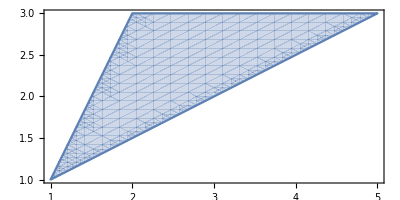

```mathematica
RegionPlot[1≤y≤3&&(y+1)/2≤x≤2y-1,{x,1,5},{y,1,3},AspectRatio->Automatic]
```

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=x^4+y^2-8 x^2-2. Enero 22

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 4 x^3-16x =4x( x^2-4) = 0 ⟹ x=0, x= 2, x=-2
		∂_y f(x,y) = 2y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (0,0), (2,0), (-2,0).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(12 x^2-16 | 0
0 | 2)|
Hessiano (0,0) = |(-16 | 0
0 | 2)|= -32 < 0 (Punto de silla)
Hessiano (2,0) = |(32 | 0
0 | 2)|= 64 > 0 (máximo o mínimo relativo) (Como ∂_(x,x) f(2,0)= 32 >0, será mínimo local)
Hessiano (-2,0) = |(32 | 0
0 | 2)|= 64 > 0 (máximo o mínimo relativo) (como ∂_(x,x) f(-2,0)=32>0, será mínimo local)

Como el hessiano en el punto (0,0) es negativo, habrá un punto de silla. Como el hessiano en los puntos (2,0) y (-2,0) es positivo habrá un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda es 32 >0, hay un mínimo relativo en esos dos puntos.
Con el Mathematica podemos dibujar la gráfica.

```mathematica
Plot3D[x^4+y^2-8x^2-2,{x,-3,3},{y,-1,1}]
```

-Graphics3D-

## 8.- Calcular los extremos absolutos (máximos y mínimos) de la función f(x,y)=x^3-2 y^2 en el conjunto de puntos que cumplen x^2+y^2≤1. Enero 22

Solución:
La función es polinómica y, por tanto, es continua y derivable. Los extremos pueden estar en el interior del círculo (x^2+y^2<1), o en el borde (en la circunferencia x^2+y^2=1).
Para encontrar los posibles puntos en el interior, hacemos derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 3 x^2 =0 ⟹ x=0
		∂_y f(x,y) = -4y = 0 ⟹ y=0
Las derivadas parciales se anulan en el punto (0,0) que está en el interior del recinto (0^2+0^2<1).

Ahora hay que estudiar los posibles puntos en el borde del recinto; cuando x^2+y^2=1. Podemos buscar los posibles puntos siguiendo dos ideas:
1) Multiplicadores de Lagrange:
Consideramos F(x,y,t) = f(x,y) + t g(x,y)
donde f(x,y)=x^3-2 y^2, g(x,y)=x^2+y^2-1.

		∂_x F(x,y,t) = 3 x^2 + t(2x) = x( 3x + 2t) = 0 
		∂_y F(x,y,t) = -4y+t(2y) = 2y(t-2) = 0
		∂_t F(x,y,t) = x^2+y^2-1 = 0
 La segunda ecuación se cumple cuando y=0 ó t=2. Consideremos cada caso:
 a) Si y=0, de la tercera ecuación sacamos que x=1 ó x=-1. En el caso x=1, la primera ecuación se cumpliría si t=-3/2. Si x =-1, la primera ecuación se cumpliría si t= 3/2. Por tanto, obtendríamos las soluciones (x,y,t)= (1,0,-3/2), (-1,0,3/2).
 b) Si t=2, la primera ecuación quedaría como  3 x^2 + 4x= x(3x+4)=0. Se cumpliría cuando x=0 ó x=-4/3. Cuando x=0, la tercera ecuación se cumpliría si y=1 ó y=-1. Cuando x=-4/3, la tercera ecuación no se cumpliría. Por tanto, obtenemos las soluciones (0,1,2) y (0,-1,2).
 
Al punto interior del círculo (0,0) debemos añadir los cuatro encontrados en el borde, (1,0), (-1,0), (0,1), (0,-1). Evaluando la función f , obtenemos:
 f(0,0)=0^3-2*0^2=0, f(1,0)=1^3-2*0^2=1, f(-1,0)=(-1)^3-2*0^2=-1, f(0,1)=0^3-2*1^2=-2, f(0,-1)=0^3-2*(-1)^2=-2.
 
El máximo absoluto se encuentra en el punto (1,0) con un valor de 1, y el mínimo absoluto se alcanza en los puntos (0,1) y (0,-1) con un valor de -2.
 
Veamos ahora otra forma de estudiar el borde.
2) Se trata de buscar los posibles máximos y mínimos de f(x,y)=x^3-2 y^2 cuando x^2+y^2=1. Podríamos despejar y^2 y sustituir en la función. Tenemos que y^2=1-x^2, por tanto  f(x,y)=x^3-2(1-x^2)=x^3+2 x^2-2 que sería una función de una variable, x. Esta variable x puede moverse en el intervalo [-1,1] (para que pueda cumplirse que x^2+y^2=1).
Los extremos de x^3+2 x^2-2, en [-1,1] se encontrarían en los extremos del intervalo o en los puntos con derivada cero. La derivada es:
3 x^2+4x = x (3x+4) =0. La derivada se anula cuando x=0 ó x=-4/3. Este último valor no pertenece al intervalo. Por tanto, nos quedamos con los valores de los extremos, x=1 y x=-1 y el punto de derivada cero, x=0. Como debe cumplirse que x^2+y^2=1, los puntos candidatos a máximos o mínimos serían: (1,0) (-1,0), (0,1) y (0,-1).

Evaluamos la función f(x,y) en los cinco puntos posibles:  
 f(0,0)=0^3-2*0^2=0, f(1,0)=1^3-2*0^2=1, f(-1,0)=(-1)^3-2*0^2=-1, f(0,1)=0^3-2*1^2=-2, f(0,-1)=0^3-2*(-1)^2=-2.

El máximo absoluto se encuentra en el punto (1,0) con un valor de 1, y el mínimo absoluto se alcanza en los puntos (0,1) y (0,-1) con un valor de -2.
Con el Mathematica dibujamos la gráfica:

```mathematica
Plot3D[Which[x^2+y^2<=1,x^3-2y^2],{x,-1,1},{y,-1,1},PlotPoints->50]
```

-Graphics3D-

## 9.- Dada la función f(x,y) = 3x^3y^2 + 2x cos y + y, calcular la ecuación del plano tangente a la gráfica de la función en el punto (1,0) y utilizarlo para estimar el valor de f(0.5, 0.5). Enero 22

Solución:
La ecuación del plano tangente a la gráfica de una función de dos variables es similar a la ecuación de la recta tangente a la gráfica de una función de una variable, añadiendo un nuevo sumando. En este caso, sería:

		z=f(1,0) + ∂_x f(1,0) (x-1)+∂_y f(1,0) (y-0)
Calculamos el valor de f en el punto y sus derivadas parciales:
f(x,y) = 3x^3y^2 + 2x cos y + y
f(1,0) = 3*1^3*0^2 + 2*1* cos 0 + 0 = 0+2+0 = 2
∂_x f(x,y)= 9x^2y^2 + 2 cos y
∂_x f(1,0)= 9*1^2*0^2 + 2 cos 0 = 2
∂_y f(x,y)= 6x^3y -2x sen y + 1
∂_y f(1,0)= 6*1^3*0 -2*1* sen 0 + 1 = 1

z=f(1,0) + ∂_x f(1,0) (x-1)+∂_y f(1,0) (y-0)= 2 + 2 (x-1)+1 (y-0)= 2 + 2x-2+y = 2x+y

El valor de f(0.5,0.5) se puede aproximar utilizando el polinomio anterior y obtenemos 2*0.5+0.5=1.5

Con el Mathematica:

```mathematica
f[x_,y_]:= 3 x^3 y^2+ 2 x Cos[y]+y
```

```mathematica
f[1,0]+(D[f[x,y],x]/.{x->1,y->0}) (x-1)+(D[f[x,y],y]/.{x->1,y->0}) (y-0)//Simplify
```

2 x+y

```mathematica
Plot3D[{f[x,y],2x+y},{x,0,1.5},{y,-1,1}]
```

-Graphics3D-

```mathematica
{f[x,y],2x+y}/.{x->0.5,y->0.5}
```

{1.47133,1.5}

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=x^3+2 y^2-3x+4. Julio 22

Solución:
La función f(x,y)=x^3+2 y^2-3x+4 es una función polinómica, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 3 x^2-3 = 3( x^2-1) = 0 ⟹ x=1, x= -1
		∂_y f(x,y) = 4y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (1,0) y (-1,0).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(6x | 0
0 | 4)|
Hessiano (1,0) = |(6 | 0
0 | 4)|= 24 > 0 (máximo o mínimo relativo) (Como ∂_(x,x) f(1,0)= 6 >0, será mínimo local)
Hessiano (-1,0) = |(-6 | 0
0 | 4)|= -24 < 0 (Punto de silla)

Como el hessiano en el punto (-1,0) es negativo, habrá un punto de silla. Como el hessiano en el punto (1,0) es positivo habrá un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda es 6 >0, hay un mínimo relativo en ese punto.

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=(x^2-4)^2+ y^2. Enero 18

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2(x^2-4)2x = 0 ⟹ x=0 ó x^2-4= 0 ⟹ x=0, 2, -2
		∂_y f(x,y) = 2y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (0,0), (2,0) y (-2,0).
Para ver si son máximos, mínimos y puntos de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(12 x^2-16 | 0
0 | 2)|
Hessiano (0,0) = |(-16 | 0
0 | 2)|= -32 < 0

Hessiano (2,0) = |(32 | 0
0 | 2)|= 64 > 0
Hessiano (-2,0) = |(32 | 0
0 | 2)|= 64 > 0

Como el hessiano en el punto (0,0) es negativo, en el punto (0,0) hay un punto de silla.

Como el hessiano en los puntos (2,0) y (-2,0) es positivo habrá un máximo o un mínimo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en esos puntos. Como la derivada segunda es 32 >0, hay mínimos relativos en esos puntos.

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)= -x^2+2x+y^2-2y+2x y + 4. Junio 21

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = -2x+2+2y = 0  ⟹ x-y=1 
		∂_y f(x,y) = 2y-2+2x = 0 ⟹ x+y=1
Resolvemos el sistema, en este caso se trata de dos ecuaciones lineales. Podemos sumar las dos ecuaciones y obtenemos x=1. Después obtenemos y=0.
 
El punto donde se anulan las dos derivadas parciales es (1,0).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(-2 | 2
2 | 2)|
Hessiano (1,0) = |(-2 | 2
2 | 2)|= -8 < 0

Como el hessiano en el punto (1,0) es negativo, en ese punto hay un punto de silla.

## 7.- Calcular los máximos y mínimos absolutos de la función f(x,y)=x^2-y^2 en el recinto dado por x^2+ 2 y^2≤ 1. Enero 19

Solución:
Los máximos o mínimos pueden estar en el interior de la elipse (cuando x^2+ 2 y^2< 1) o en el borde (x^2+ 2 y^2= 1).
Para el interior, hacemos derivadas parciales y calculamos dónde se anulan:
∂_x f= 2x=0, ∂_y f= -2y=0 ⟹ x=0, y=0. Las derivadas parciales se anulan en el punto (0,0) que está dentro de la elipse pues  0^2+ 2*0^2< 1.
Respecto al borde utilizamos la técnica de los multiplicadores de Lagrange. Para ello consideramos F(x,y,λ)=x^2-y^2 + λ(x^2+ 2 y^2- 1). Haciendo derivadas parciales e igualando a cero tenemos:
∂_x F= 2x +2xλ=0 ⟹x(1+λ)=0 
∂_y F= -2y + 4yλ=0  ⟹y(-1+2λ)=0  
∂_λ F= x^2+ 2 y^2- 1=0
De la primera ecuación, una posibilidad es x=0. En este caso, de la tercera ecuación, y=±√(1/2). Con lo cual, para que se cumpla también la segunda ecuación λ debe ser 1/2. Obtenemos así unos puntos posibles (0,√(1/2)),  (0,-√(1/2)).
De la primera ecuación, si x no es cero, tenemos que λ=-1, entonces la segunda ecuación quedaría como -3y=0. Por tanto, y=0. Ahora en la tercera ecuación, x=±1. Por tanto aparecen los puntos (1,0) y (-1,0).
Juntando los cinco puntos candidatos, evaluamos la función f en ellos y obtenemos:
f(0,0)=0, f(1,0)=1, f(-1,0)=1, f(0,√(1/2))=-1/2,  f(0,-√(1/2))=-1/2.
De donde concluimos que f, en el recinto dado, tiene máximos absolutos en (1,0) y (-1,0) y mínimos absolutos en (0,√(1/2)) y  (0,-√(1/2)).

## 8.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=(x^2(x-2))^2+ y^2. Enero 19

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2(x(x-2))^2 + 2x^2(x-2)= 2x(x-2)(x-2+x) =0 ⟹ x=0, (x-2)=0 ó (x-2+x)=0 ⟹ x=0, 2, 1
		∂_y f(x,y) = 2y = 0 ⟹ y=0
Los puntos donde se anulan las dos derivadas parciales son (0,0), (2,0) y (1,0).
Para ver si son máximos, mínimos y puntos de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(12 x^2-24x+8 | 0
0 | 2)|
Hessiano (0,0) = |(8 | 0
0 | 2)|= 16 > 0

Hessiano (2,0) = |(8 | 0
0 | 2)|= 16 > 0
Hessiano (1,0) = |(-4 | 0
0 | 2)|= -8 < 0

Como el hessiano en los puntos (0,0) y (2,0) es positivo habrá un máximo o un mínimo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en esos puntos. Como la derivada segunda es 8 >0, hay mínimos relativos en esos puntos.

Como el hessiano en el punto (1,0) es negativo, en el punto (1,0) hay un punto de silla.

## 7.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)=x^2+2x+y^2-4y+8. Enero 21

Solución:
La función f es un polinomio, por tanto es derivable todas las veces que queramos y en todos los puntos del plano. Para buscar los puntos que podrían ser extremos calculamos las derivadas parciales e igualamos a cero.
		∂_x f(x,y) = 2x+2 = 0 ⟹ x= -1
		∂_y f(x,y) = 2y-4 = 0 ⟹ y=2
El punto donde se anulan las dos derivadas parciales es (-1,2).
Para ver si es máximo, mínimo o punto de silla calculamos el hessiano.

Hessiano (x,y) = |(∂_(x,x) f(x,y) | ∂_(x,y) f(x,y)
∂_(x,y) f(x,y) | ∂_(y,y) f(x,y))|= |(2 | 0
0 | 2)|
Hessiano (-1,2) = |(2 | 0
0 | 2)|= 4 > 0

Como el hessiano en el punto (-1,2) es positivo, en ese punto hay un mínimo o un máximo relativo. Para saber si es máximo o mínimo vemos la derivada segunda en x (o en y) en ese punto. Como la derivada segunda es 2 >0, hay un mínimo relativo en ese punto.

## 6.- Calcular los extremos relativos (máximos, mínimos y puntos de silla) de la función f(x,y)= x^4 + y^4 - 4xy +1. Enero 20

Solución: Calculamos las derivadas parciales e igualamos a 0,
∂_x f[x,y] = 4 x^3-4 y = 0
∂_y f[x,y] = -4 x+4 y^3 = 0
Resolvemos el sistema, y=x^3, x=y^3, por tanto, x=y^3=x^9, de donde x(1-x^8)=0, x=0, 1, -1. Los puntos donde se anulan las derivadas parciales son (0,0), (1,1), (-1,-1).
Haciendo las derivadas segundas,
∂_(x,x) f[x,y] = 12 x^2
∂_(x,y) f[x,y] = -4
∂_(y,x) f[x,y] = -4
∂_(y,y) f[x,y] = 12 y^2 
Hess(x,y)=(12 x^2 | -4
-4 | 12 y^2) 
En el punto (0,0) el determinante es negativo, por tanto hay un punto de silla. En los puntos (1,1) y (-1,-1), el determinante es positivo y la derivada segunda respecto a x, es positiva, luego son mínimos relativos.

## 6.- Calcular la integral de la función f(x,y)= x^2+y en el rectángulo de vértices (0,0), (2,0), (0,1) y (2,1). Enero 21

Solución:
∫_0^2 (∫_0^1 x^2+yⅆy)ⅆx= ∫_0^2 (x^2 y+y^2/2)|_(y=0)^(y=1)ⅆx =  ∫_0^2 (x^2*1+1^2/2- (x^2*0+0^2/2))ⅆx =  ∫_0^2 (x^2+1/2)ⅆx = (x^3/3+x/2)|_(x=0)^(x=2) = (2^3/3+2/2)- (0^3/3+0/2)= (8/3+1)=11/3

## 6.- Calcular la integral de la función f(x,y)= x^2+y en el triángulo de vértices (-1,0), (0,2) y (1,0). Junio 21

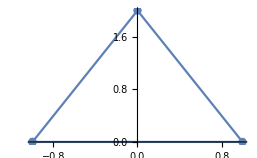
Solución:
Observamos el triángulo determinado por los puntos que nos da el problema.
-Graphics-
Las rectas que delimitan el triángulo son y=0, y=2x+2, y=2-2x.
Podríamos calcular la integral de dos formas. 
1) Observamos que la variable x varía entre -1 y 1. Para cada valor de x entre -1 y 0, la variable y varía entre 0 y 2x+2. En cambio, para cada valor de x entre 0 y 1, la variable y se mueve entre 0 y 2-2x.
2) Por otra parte, si pensamos que la variable y se mueve entre 0 y 2, podemos ver que la variable x está entre (y-2)/2 y (2-y)/2.

Así, siguiendo la primera vía la integral sería:

 ∫_-1^0 (∫_0^(2x+2) x^2+yⅆy)ⅆx + ∫_0^1 (∫_0^(-2x+2) x^2+yⅆy)ⅆx.
 
 Realizamos los cálculos:

 ∫_-1^0 (∫_0^(2x+2) x^2+yⅆy)ⅆx= ∫_-1^0 (x^2 y+y^2/2)|_(y=0)^(y=2x+2)ⅆx =  ∫_-1^0 (x^2*(2x+2)+(2x+2)^2/2- (x^2*0+0^2/2))ⅆx =  ∫_-1^0 (2 x^3+ 2 x^2+2 x^2+4x+2)ⅆx =   ∫_-1^0 (2 x^3+ 4 x^2+4x+2)ⅆx = x^4/2+ 4 x^3/3+2 x^2+2x|_(x=-1)^(x=0) = (0^4/2+ 4 0^3/3+2*0^2+2*0) - ((-1)^4/2+ 4(-1)^3/3+2(-1)^2+2(-1)) = -1/2+4/3-2+2 = (-3+8)/6= 5/6.

∫_0^1 (∫_0^(-2x+2) x^2+yⅆy)ⅆx= ∫_0^1 (x^2 y+y^2/2)|_(y=0)^(y=-2x+2)ⅆx =  ∫_0^1 (x^2*(-2x+2)+(-2x+2)^2/2- (x^2*0+0^2/2))ⅆx =  ∫_0^1 (-2 x^3+ 2 x^2+2 x^2-4x+2)ⅆx =   ∫_0^1 (-2 x^3+ 4 x^2-4x+2)ⅆx = -x^4/2+ 4 x^3/3-2 x^2+2x|_(x=0)^(x=1) = (-1^4/2+ 4 1^3/3-2*1^2+2*1) - (-0^4/2+ 4 0^3/3.2*0^2+2*0) = -1/2+4/3-2+2 = (-3+8)/6= 5/6.

El resultado sería  5/6 +  5/6 =  10/6 =  5/3

Siguiendo la segunda vía tendríamos:

∫_0^2 (∫_((y-2)/2)^((2-y)/2) x^2+yⅆx)ⅆy= ∫_0^2 (x^3/3+y x)|_(x=(y-2)/2)^(x=(2-y)/2)ⅆy =  ∫_0^2 (((2-y)/2)^3/3+y (2-y)/2- (((y-2)/2)^3/3+y (y-2)/2 ))ⅆy =  ∫_0^2 ((2-y)^3/24+(2y-y^2)/2 -(y-2)^3/24-(y^2-2y)/2 )ⅆy =  ∫_0^2 (2-y)^3/12+(2y-y^2) ⅆy= -(2-y)^4/48+y^2-y^3/3|_(y=0)^(y=2) = -(2-2)^4/48+2^2-2^3/3+(2-0)^4/48-0^2+0^3/3 =  4-8/3+16/48 =4-8/3+1/3=4-7/3 = 5/3

## 6.- Calcular el valor de la integral de la función f(x,y) = x+2y en el paralelogramo de vértices (1,1), (2,1), (2,2), (3,2). Junio 18

## 3.- Calcular la integral de la función f(x,y)= 1-x-y en el triángulo de vértices (0,0), (1,0) y (0,1), para obtener el volumen de la siguiente figura. -Graphics3D-Integral: ENERO 18, PRÁCTICAS

Solución:
Siguiendo lo explicado en Prácticas, sobre integrales dobles:

```mathematica
∫_0^1 (∫_0^(1-x) (1-x-y)ⅆy)ⅆx
```

1/6

## 3.- Calcular la integral de la función f(x,y)= x^2+y^2 en el triángulo de vértices (0,0), (1,0) y (0,1), para obtener el volumen de la siguiente figura. -Graphics3D- Integral: ENERO 18, PRÁCTICAS

Solución: Seguimos lo que aparece en Prácticas:
El conjunto donde tenemos que realizar la integral es el triángulo de vértices (0,0), (1,0) y (1,1).

```mathematica
RegionPlot[0≤x≤1&&0≤y≤x,{x,0,1},{y,0,1},AspectRatio->Automatic]
```

-Graphics-

En este caso, podemos considerar una cualquiera de las variables, por ejemplo la x. La variable x se mueve entre 0 y 1. Una vez fijado el valor de x, entre 0 y 1. El valor de y se moverá entre 0 y x. La variable y se movería desde el 0 hasta el punto de la recta que une (0,0) y (1,1). Se trata de la recta y=x.

```mathematica
∫_0^1 ∫_0^x (x^2+y^2)ⅆyⅆx
```

1/3

3.- Calcular ∫∫_D (x^2-y^2)ⅆyⅆx siendo D el recinto comprendido entre las gráficas de y = (a+1) x e y = x^2, siendo a el último dígito numérico de su DNI.
	Integral:

3.- La integral de la función f(x,y)= x^2+2 y^2 en el triángulo de vértices (0,0), (1,0) y (0,1) es.




1)  5/12, 2) 1/3, 3) 2,  4) 13/18, 5) 1/4

ENERO 19, PRÁCTICAS
3.- Calcular la integral de la función f(x,y)= x^2+y^2 en el cuadrilátero de vértices (0,0), (1,0), (2,1) y (1,1), 
Integral:

Solución: El recinto es el cuadrilátero . Para calcular la integral, tenemos que las ecuaciones de las rectas de los lados son y=x, y=x-1, y=0, y=1. Parece más sencillo decir que la y varía entre 0 y 1, y para cada valor de y, la x varía entre y e y+1.

```mathematica
∫_0^1 (∫_y^(y+1) (x^2+y^2)ⅆx)ⅆy
```

3/2

3.- Calcular la integral de la función f(x,y)= 1-x-y en el triángulo de vértices (0,0), (1,0) y (0,1), para obtener el volumen de la siguiente figura.
-Graphics3D-Integral:

Solución: El recinto es el triángulo . Para calcular la integral, tenemos que las ecuaciones de las rectas de los lados son y=1-x, y=0, x=0. Podemos plantear cualquiera de las dos integrales dobles con similar dificultad. Si por ejemplo tomamos que x varía de 0 a 1, la y variará entre 0 y 1-x.

```mathematica
∫_0^1 (∫_0^(1-x) (1-x-y)ⅆy)ⅆx
```

1/6

3.- Calcular la integral de la función f(x,y)= x^2+2 y^2 en el cuadrilátero de vértices (0,0), (1,0), (2,1) y (1,1), 
Integral:

Solución: El recinto es el cuadrilátero . Para calcular la integral, tenemos que las ecuaciones de las rectas de los lados son y=x, y=x-1, y=0, y=1. Parece más sencillo decir que la y varía entre 0 y 1, y para cada valor de y, la x varía entre y e y+1.

```mathematica
∫_0^1 (∫_y^(y+1) (x^2+2 y^2)ⅆx)ⅆy
```

11/6

3.- Calcular la integral de la función f(x,y)= 2 x^2+y^2 en el cuadrilátero de vértices (0,0), (1,0), (2,1) y (1,1), 
Integral:

Solución: El recinto es el cuadrilátero . Para calcular la integral, tenemos que las ecuaciones de las rectas de los lados son y=x, y=x-1, y=0, y=1. Parece más sencillo decir que la y varía entre 0 y 1, y para cada valor de y, la x varía entre y e y+1.

```mathematica
∫_0^1 (∫_y^(y+1) (2 x^2+y^2)ⅆx)ⅆy
```

8/3

5.- Calcular los máximos y mínimos absolutos de la función f(x,y)=2 x^2- y^2 en el recinto dado por x^2+ y^2≤ 1.

## MÁS EJERCICIOS • Calcular los extremos relativos de la función: ▪ f(x,y) = xy + 2/x+ 4/y ▪ f(x,y) = e^(- (x^2+ y^2 - 4y )) ▪ f(x,y) = x^2 + 4 y^2 - 2x + 8y - 1 • Calcular los extremos de la función ▪ f(x,y) =y^2 - x^2 en x^2/4+ y^2 = 1 ▪ f(x,y) = x^2 + y^2 en xy -3 = 0 ▪ f(x,y) = x^2 + 4xy + y^2 en x - y - 6 = 0 • Calcular el gradiente de f(x,y)=x^2y - x y^2 en el punto P=(-2,3). • Calcular el plano tangente a z= -10√xy en (1,-1) • Calcular el plano tangente a 2 z^2 + x^2 + y^2 = 23 en (1,2,3) • Calcular el plano tangente a z=xe^(- 2y) en (1,0,1) • Calcular el volumen de la figura limitada por arriba por la gráfica de f(x,y) = x^2 + y^2 , y en el plano por las rectas x=1, x=3, y=0, y=1. • Calcular las siguientes integrales: ▪ ∫_-1^2 ∫_3^6 10 x y^2 ⅆyⅆx ▪∫_0^1 ∫_1^3 ∫_-1^2 ( 2x +3y -z)ⅆxⅆyⅆz ▪ ∫_1^2 ∫_0^(x - 1) yⅆyⅆx ▪ ∫_-3^1 ∫_0^x 3/(x^2 + y^2)ⅆyⅆx ▪ ∫_0^2 ∫_0^(√(4 - x^2)) ( x+y)ⅆxⅆy ▪ Integral de la función f(x,y) = e^(y^2) en la región R={(x,y) / 0≤x≤2y, 0≤y≤2 }